# Αριθμητική Επίλυση Προβλημάτων Κβαντομηχανικής

## Εργασία στο μάθημα [ΓΘΕ204] Προβλήματα Κβαντικής Φυσικής

Ρουμπάς Κωνσταντίνος - ΑΕΜ: 14652

## Εύρεση Ριζών

Η γενική μορφή θα μοιάζει κάπως έτσι:

```mathematica
f[x_]=…;
xi=…;
While[Round[N[f[xi],12]]!=0,
xi=xi-f[xi]/f'[xi]]
Print[N[xi,12]]
```

Που την κατασκευάσαμε ώστε να λειτουργεί σαν την εντολή:

```mathematica
FindRoot[{f[x]==0},{x,xi}]
```

### Εφαρμογή:

Στο πρόβλημα του ορθογώνιου φρέατος δυναμικού, καταλήγουμε σε δύο υπερβατικές εξισώσεις:

√(C(E+Vo))tan[√(C(E+Vo))L]=√-CE, για τις άρτιες καταστάσεις

-√(C(E+Vo))cot[√(C(E+Vo))L]=√-CE , για τις περιττές.

Με αριθμητικές τιμές των C, Vo, L και R, όπου R^2=CL^2 Vo

```mathematica
c=26.247;v0=300;L=0.2;radius=Sqrt[c*v0*L^2];
```

```mathematica
eta[xi_]:= Sqrt[radius^2 - xi^2]/;xi <= radius; eta[xi_]:= 0/; xi > radius;
etaEven[xi_]:= xi * Tan[xi]; etaOdd[xi_]:= -xi * Cot[xi];
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

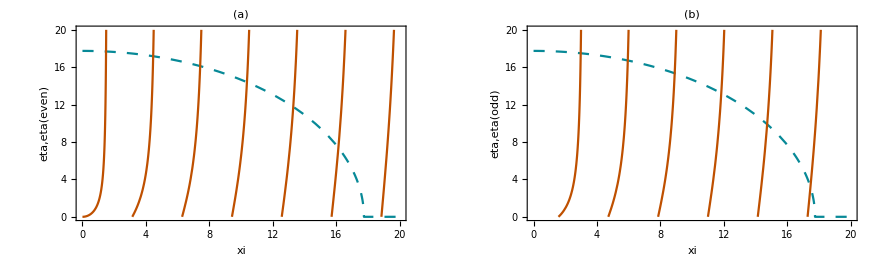

```mathematica
EvenState = Plot[ {eta[xi], etaEven[xi]}, {xi, 0, 20},
				PlotRange -> {{0,20},{0,20}},Frame-> True,
				PlotStyle -> {{Dashing[{0.02}]}, {Thickness[0.004]}},
				FrameLabel -> {"xi","eta,eta(even)"},
				PlotLabel -> "(a)"];
OddState = Plot[ {eta[xi],etaOdd[xi]},{xi, 0, 20},
				PlotRange ->{{0,20},{0,20}},Frame->True,
				PlotStyle-> {{Dashing[{0.02}]},{Thickness[0.004]}},
				FrameLabel ->{"xi","eta,eta(odd)"},
				PlotLabel ->"(b)" ];
Show[ GraphicsArray[{EvenState,OddState}] ]
```

```mathematica
xieta={{1.46255,17.7328},{4.43098,17.2205},{7.4192,16.1958},{10.3481,14.4347},{13.2769,11.745},{16.1266,7.42231}} ;(*προσέγγιση του σημείου τομής από τη γραφική λύση*)
evenEnergyGraph=Table[-xieta[[i,2]]^2/(L^2*c),{i,1,6}];
evenEnergy=Table[Null,20];
Timing[
Do[ estart=evenEnergyGraph[[i]];
	 en=FindRoot[Sqrt[c*(e+v0)]*Sin[Sqrt[c*(e+v0)]*L]
	 ==Sqrt[-c*e]*Cos[Sqrt[c*(e+v0)]*L],{e,estart}];
	 evenEnergy[[i]]=e/.en; ex= evenEnergy[[i]];
	 test = Sqrt[c*(ex+v0)]*Tan[Sqrt[c*(ex+v0)]*L]-Sqrt[-c*ex];
	 Print["evenEnergy[",i,"]=",evenEnergy[[i]]," test[",i,"]=",test],{i,1,6}];]
```

evenEnergy[1]=-297.894 test[1]=8.3844×10^-13

evenEnergy[2]=-281.067 test[2]=-2.4869×10^-12

evenEnergy[3]=-247.524 test[3]=1.13687×10^-13

evenEnergy[4]=-197.544 test[4]=2.98428×10^-13

evenEnergy[5]=-131.748 test[5]=-4.9738×10^-14

evenEnergy[6]=-51.9626 test[6]=2.27374×10^-13

{0.,Null}

Πάμε, αντί για την FindRoot να χρησιμοποιήσουμε το δικό μας πρόγραμμα, με

```mathematica
xieta={{1.46255,17.7328},{4.43098,17.2205},{7.4192,16.1958},{10.3481,14.4347},{13.2769,11.745},{16.1266,7.42231}} ;(*προσέγγιση του σημείου τομής από τη γραφική λύση*)
evenEnergyGraph=Table[-xieta[[i,2]]^2/(L^2*c),{i,1,6}];
evenEnergy=Table[Null,20];
f[e_]=Sqrt[c*(e+v0)]*Sin[Sqrt[c*(e+v0)]*L]-Sqrt[-c*e]*Cos[Sqrt[c*(e+v0)]*L]; (* f[x_]=… *)
Timing[
Do[ estart=evenEnergyGraph[[i]]; (* xi=… *)
	 While[Round[N[f[estart]],0.00000000001]!=0,
		estart=estart-f[estart]/f'[estart]];
	evenEnergy[[i]]=estart; ex= evenEnergy[[i]];
	test = Sqrt[c*(ex+v0)]*Tan[Sqrt[c*(ex+v0)]*L]-Sqrt[-c*ex];
	Print["evenEnergy[",i,"]=",evenEnergy[[i]]," test[",i,"]=",test],{i,1,6}];]
```

evenEnergy[1]=-297.894 test[1]=8.3844×10^-13

evenEnergy[2]=-281.067 test[2]=-2.4869×10^-12

evenEnergy[3]=-247.524 test[3]=1.13687×10^-13

evenEnergy[4]=-197.544 test[4]=2.98428×10^-13

evenEnergy[5]=-131.748 test[5]=-4.9738×10^-14

evenEnergy[6]=-51.9626 test[6]=-4.4551×10^-12

{0.,Null}

## Αριθμητική Ολοκλήρωση

```mathematica
NIntegrate[…,Method->];
```

### Τύποι Newton-Cotes

#### Κανόνας του Τραπεζίου

```mathematica
x1 = …; x2 = …;
f1 = …; f2 = …;
int = (x2 - x1) (f1 + f2)/2
```

#### Τύπος του Simpson

```mathematica
x1=…;x2=…;
f1=…;f12=…;f2=…;
int = ((x2-x1)/2)[1/3 f1+4/3 f12+1/3 f2]
```

### Μέθοδος Gauss

```mathematica
t1 = …; …;
c1 = …; …;
a0 = …; …;
int = c1 (a0 + a1 x1 + a2 x2^2 + a3 x3^3 + …) + c2 (a0 + a1 x1 + a2 x2^2 + a3 x3^3 + …) + …;
```

### Εφαρμογή:

Υπολογισμός Πληροφοριακής εντροπίας για τις n=20 πρώτες καταστάσεις:

```mathematica
Clear[n];
f[xi_,n_]=(1-(-1)^n Cos[xi])/((n Pi-xi)^2(n Pi+xi)^2) Log[(1-(-1)^n Cos[xi])/((n Pi-xi)^2(n Pi+xi)^2)];
n=1;
Do[int=NIntegrate[f[xi,2n],{xi,-∞,+∞}];Print["int=",int," n=",n];n=n+1;,{i,20}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xi near {xi} = {169.667}. NIntegrate obtained -0.244224 and 3.3779×10^-7 for the integral and error estimates.

int=-0.244224 n=1

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xi near {xi} = {169.667}. NIntegrate obtained -0.0770561 and 2.88374×10^-7 for the integral and error estimates.

int=-0.0770561 n=2

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xi near {xi} = {169.667}. NIntegrate obtained -0.0381776 and 3.52236×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

int=-0.0381776 n=3

int=-0.0230048 n=4

int=-0.0154721 n=5

int=-0.0111653 n=6

int=-0.00846289 n=7

int=-0.00665087 n=8

int=-0.00537412 n=9

int=-0.00443908 n=10

int=-0.00373283 n=11

int=-0.00318575 n=12

int=-0.00275296 n=13

int=-0.0024044 n=14

int=-0.00211937 n=15

int=-0.00188312 n=16

int=-0.00168506 n=17

int=-0.00151731 n=18

int=-0.0013739 n=19

int=-0.00125036 n=20

```mathematica
Clear[n];
h[xi_,n_]=Sqrt[1+xi^2]^3 f[xi,n];
Simplify[Series[h[xi,n],{xi,0,4}]]
```

-((-1+(-1)^n) Log[(1+(-1)^(1+n))/(n^4 π^4)])/(n^4 π^4)+((4-4 (-1)^n+(-1)^n n^2 π^2+(4-4 (-1)^n-(-3+2 (-1)^n) n^2 π^2) Log[(1+(-1)^(1+n))/(n^4 π^4)]) xi^2)/(2 n^6 π^6)+1/(24 (-1+(-1)^n) n^8 π^8)(-120 (-1+(-1)^n)^2-24 (3-4 (-1)^n+(-1)^(2 n)) n^2 π^2+(-1)^n (-17+14 (-1)^n) n^4 π^4+(-72 (-1+(-1)^n)^2-24 (3-5 (-1)^n+2 (-1)^(2 n)) n^2 π^2+(-9+(-1)^n+8 (-1)^(2 n)) n^4 π^4) Log[(1+(-1)^(1+n))/(n^4 π^4)]) xi^4+O[xi]^5

```mathematica
c1=(18-Sqrt[30])/36;c2=(18+Sqrt[30])/36;c3=(18+Sqrt[30])/36;c4=(18-Sqrt[30]);
x1=-Sqrt[525+70Sqrt[30]]/35;x2=-Sqrt[525-70Sqrt[30]]/35;x3=Sqrt[525+70Sqrt[30]]/35;x4=Sqrt[525-70Sqrt[30]]/35;
a0=-((-1+(-1)^n) Log[(1+(-1)^(1+n))/(n^4 π^4)])/(n^4 π^4);
a1=0.0 ;a2(4-4 (-1)^n+(-1)^n n^2 π^2+(4-4 (-1)^n-(-3+2 (-1)^n) n^2 π^2) Log[(1+(-1)^(1+n))/(n^4 π^4)])/(2 n^6 π^6);
a3=0.0  ;a4=1/(24 (-1+(-1)^n) n^8 π^8)(-120 (-1+(-1)^n)^2-24 (3-4 (-1)^n+(-1)^(2 n)) n^2 π^2+(-1)^n (-17+14 (-1)^n) n^4 π^4+(-72 (-1+(-1)^n)^2-24 (3-5 (-1)^n+2 (-1)^(2 n)) n^2 π^2+(-9+(-1)^n+8 (-1)^(2 n)) n^4 π^4) Log[(1+(-1)^(1+n))/(n^4 π^4)]);
```

```mathematica
Clear[int,n];
n=1;
Do[
	int=c1*(a0+a1*x1+a2*x1^2+a3*x1^3+a4*x1^4)+
	c2*(a0+a1*x2+a2*x2^2+a3*x2^3+a4*x2^4)+
	c3*(a0+a1*x3+a2*x3^2+a3*x3^3+a4*x3^4)+
	c4*(a0+a1*x4+a2*x4^2+a3*x4^3+a4*x4^4);
	Print["int=",N[int]," n=",n];n=n+1,{i,20}]
```

int=-1.41424 n=1

Infinity::indet: Indeterminate expression (0 (-∞))/π^4 encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

Infinity::indet: Indeterminate expression (0 (-∞))/π^4 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

int=Indeterminate n=2

int=-0.0360603 n=3

int=Indeterminate n=4

int=-0.00580657 n=5

int=Indeterminate n=6

int=-0.00170653 n=7

int=Indeterminate n=8

int=-0.000677901 n=9

int=Indeterminate n=10

int=-0.000322906 n=11

int=Indeterminate n=12

int=-0.000173693 n=13

int=Indeterminate n=14

int=-0.000101939 n=15

int=Indeterminate n=16

int=-0.0000638818 n=17

int=Indeterminate n=18

int=-0.0000421332 n=19

int=Indeterminate n=20

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^2 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

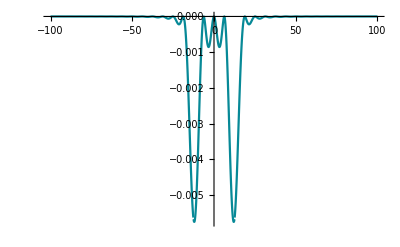

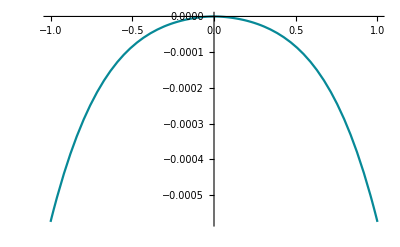

int=-0.246397 n=1

int=-0.00367699 n=2

int=-0.00602964 n=3

int=-0.000297137 n=4

int=-0.000966813 n=5

int=-0.0000667643 n=6

int=-0.000283733 n=7

int=-0.000022957 n=8

int=-0.000112628 n=9

int=-9.98836×10^-6 n=10

int=-0.0000536249 n=11

int=-5.04813×10^-6 n=12

int=-0.0000288365 n=13

int=-2.83055×10^-6 n=14

int=-0.0000169202 n=15

int=-1.71295×10^-6 n=16

int=-0.0000106015 n=17

int=-1.099×10^-6 n=18

int=-6.99124×10^-6 n=19

int=-7.38441×10^-7 n=20

```mathematica
Plot[f[x,4],{x,-100,100},PlotRange->All]
Plot[h[x,4],{x,-1,1},PlotRange->All]
Clear[n];
n=1;
Do[int=NIntegrate[h[xi,n],{xi,-1,+1}];Print["int=",int," n=",n];n=n+1;,{i,20}]
```

#### Κανόνας του Τραπεζίου

```mathematica
x1 = -1; x2 =1;
n=1;
f1 = h[-1,n]; f2 = h[1,n];
Do[
	int = (x2 - x1) (f1 + f2)/2; Print["int= ",N[int]," n= ", n]; n=n+1;
	f1 = h[-1,n]; f2 = h[1,n];,{i,20}]
```

int= -0.43564 n= 1

int= -0.0141868 n= 2

int= -0.0096229 n= 3

int= -0.00115 n= 4

int= -0.00152607 n= 5

int= -0.000259304 n= 6

int= -0.000446168 n= 7

int= -0.000089383 n= 8

int= -0.00017677 n= 9

int= -0.0000389602 n= 10

int= -0.000084067 n= 11

int= -0.0000197181 n= 12

int= -0.0000451709 n= 13

int= -0.0000110685 n= 14

int= -0.0000264892 n= 15

int= -6.70445×10^-6 n= 16

int= -0.0000165896 n= 17

int= -4.30479×10^-6 n= 18

int= -0.0000109362 n= 19

int= -2.89441×10^-6 n= 20

#### Τύπος του Simpson

```mathematica
x1 = -1; x2 =1;
n=1;
f1 = h[-1,n];f12=h[0,n]; f2 = h[1,n];
Do[
	int = ((x2-x1)/2)[1/3 f1+4/3 f12+1/3 f2];Print["int= ",N[int]," n= ", n]; n=n+1;f1 = h[-1,n]; 
	f2 = h[1,n];f12=h[0,n],{i,20}]
```

int= 1.[-0.25159] n= 1

Infinity::indet: Indeterminate expression (0 (-∞))/(4 4 π^2 π^2) encountered.

int= 1.[Indeterminate] n= 2

int= 1.[-0.00600614] n= 3

Infinity::indet: Indeterminate expression (0 (-∞))/(16 16 π^2 π^2) encountered.

int= 1.[Indeterminate] n= 4

int= 1.[-0.000960875] n= 5

Infinity::indet: Indeterminate expression (0 (-∞))/(36 36 π^2 π^2) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

int= 1.[Indeterminate] n= 6

int= 1.[-0.000281776] n= 7

int= 1.[Indeterminate] n= 8

int= 1.[-0.000111809] n= 9

int= 1.[Indeterminate] n= 10

int= 1.[-0.0000532225] n= 11

int= 1.[Indeterminate] n= 12

int= 1.[-0.0000286156] n= 13

int= 1.[Indeterminate] n= 14

int= 1.[-0.0000167886] n= 15

int= 1.[Indeterminate] n= 16

int= 1.[-0.0000105181] n= 17

int= 1.[Indeterminate] n= 18

int= 1.[-6.93577×10^-6] n= 19

int= 1.[Indeterminate] n= 20